# Homework #7

Global Constants

```mathematica
g=9.8;
```

## Problem 1

```mathematica
Clear[m1,m2,v1,v2]
```

```mathematica
m1:=1200
m2:=1800
v1:=12
v2:=20
```

Center of mass position relative to first car

```mathematica
40-(m1*0+m2*40)/(m1+m2)
```

16

Total Momentum

```mathematica
m1*v1+m2*v2
```

50400

Speed of C.O.M

```mathematica
(m1*v1+m2*v2)/(m1+m2)//N
```

16.8

## Problem 2

```mathematica
Clear[com,x1,x2,m1,ℛm,ℛv]
```

```mathematica
com:=2
x1:=8
x2:=0
m1:=0.1
v1:=0
```

```mathematica
ℛm=NSolve[
com==(m2*x2+m1*x1)/(m2+m1),m2
]
```

{{m2→0.3}}

```mathematica
ℛv=Solve[
5==(m1*v1+m2*v2)/(m1+m2),v2
]/.ℛm
```

{{{v2→6.66667}}}

Total Momentum

```mathematica
m1*v1+m2*v2/.ℛm/.ℛv
```

{{{2.}}}

## Problem 3

Use positive value for James Speed

```mathematica
With[{mj=95,mr=69,vr=1.1},
Solve[
0==mr*vr+mj*vj,vj
]
]
```

{{vj→-0.798947}}

## Problem 4

```mathematica
Clear[dL,mL,mB,mE]
```

In general any motion of particles in a system with no external forces obeys

```mathematica
dL:=3.4
mL:=280
mB:=28
mE:=45
```

```mathematica
Solve[
0==mB*dx+mL*dx+mE*(dx-dL),dx
]//N
```

{{dx→0.433428}}

## Problem 5

```mathematica
Clear[mW,mC,dC]
```

```mathematica
mW:=45
mC:=60
dC:=5
```

```mathematica
Solve[
(dC/2*mC+mW)/(mC+mW)==(mW*(4-x)+mC*(2.5-x))/(mC+mW)
]
```

{{x→1.28571}}

## Problem 6

```mathematica
Clear[M,v0,ϕ,ℛv,ℛt]
```

```mathematica
M=20;
v0=80;
ϕ=60Degree;
```

Conservation of momentum to find velocity of 2nd shard

```mathematica
ℛv=Solve[
M*v0*Cos[ϕ]==M/2*v
]
```

{{v→80}}

Time till both shards hit the ground

```mathematica
ℛt=Solve[
v*Sin[ϕ]-g*t==0,t
]/.ℛv
```

{{{t→7.0696}}}

Distance from firing of moving shard

```mathematica
(v*Cos[ϕ]+v0)*t/.ℛv/.ℛt//Flatten//First
```

848.351

Change in energy from explosion

```mathematica
1/2*M/2*v^2-1/2*M*(v0*Cos[ϕ])^2/.ℛv//Flatten//First
```

16000

## Problem 7

```mathematica
Clear[ℛθ]
```

```mathematica
ℛθ=Solve[
1.52==(2.47)*θ
]
```

{{θ→0.615385}}

```mathematica
θ/Degree/.ℛθ
```

{35.2589}

```mathematica
Solve[
13.2==r*(127Degree),r
]
```

{{r→5.95515}}

```mathematica
Solve[
s==1.47*0.65,s
]
```

{{s→0.9555}}

## Problem 8

```mathematica
Clear[γ,β,ω,α]
```

```mathematica
ω[t_]:=γ-β*t^2
```

```mathematica
α[t_]=D[ω[t],t]
```

-2 t β

```mathematica
γ:=5.5
β:=0.75
```

```mathematica
α[2.5]
```

-3.75

```mathematica
αAVG=(ω[2.5]-ω[0])/2.5
```

-1.875

## Problem 9

```mathematica
Clear[dθ,ω,α]
```

```mathematica
With[{a=0.5,b=0.250,c=2},
ω[t_]:=a*t-b*Sin[c*t]
]
```

Angular displacement of paint from 0 to 2 seconds

```mathematica
dθ=Integrate[ω[t],{t,0,x}]/.{x->2}
```

0.793295

In Degrees

```mathematica
dθ/Degree
```

45.4524

Distance displaced

```mathematica
dθ*50
```

39.6647

```mathematica
D[ω[t],t]
```

0.5-0.5 Cos[2 t]

```mathematica
α[t_]:=0.5-0.5* Cos[2 t]
```

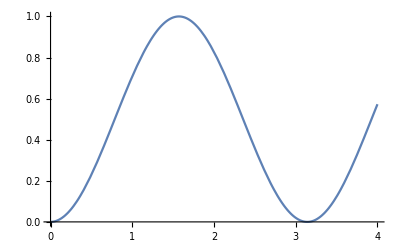

```mathematica
Plot[α[t],{t,0,4}]
```

## Problem 10

```mathematica
Clear[ω]
```

```mathematica
ω[t_]:=-6+(10/14)*t
```

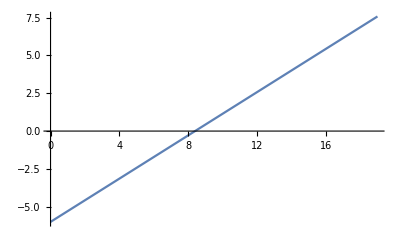

```mathematica
Plot[ω[t],{t,0,19}]
```

```mathematica
NSolve[ω[t]==0,t]
```

{{t→8.4}}

```mathematica
Integrate[ω[t],{t,0,14}]
```

-14

## Problem 11

```mathematica
Clear[ω]
```

```mathematica
ω[t_]:=500/60+((150-500)/60)/5*t
```

```mathematica
D[ω[t],t]//N
```

-1.16667

```mathematica
Integrate[ω[t],{t,0,x}]/.{x->5}//N
```

27.0833

```mathematica
Solve[ω[t+5]==0]//N
```

{{t→2.14286}}

## Problem 12

```mathematica
Clear[ω,ω0,ω1,ω2,t0]
```

```mathematica
ω1[t_]:=28+25*t
```

```mathematica
ω0=ω1[1.8]
```

73.

```mathematica
ω2[t_]:=ω0-ω0/t0*t
```

```mathematica
ℛt=Solve[
Integrate[ω2[t],{t,0,t0}]==432
]
```

{{t0→11.8356}}

```mathematica
Integrate[ω1[t],{t,0,1.9}]+432
```

530.325

```mathematica
-ω0/t0/.ℛt
```

{-6.16782}

## Problem 14

and

```mathematica
0.2/(2.5/2)*60/(2*π)
```

```mathematica
(1/8*9.8)/(2.5/2)
```

0.98

```mathematica
Solve[
2.75==2.5/2*θ,θ
]
```

{{θ→2.2}}

```mathematica
2.2/Degree
```

126.051

## Problem 15

Innermost

```mathematica
1.25/(25*10^-3)
```

50.

Outermost

```mathematica
1.25/(58*10^-3)
```

21.5517

CD Length Stretched

```mathematica
(74*60*1.25)/1000
```

5.55

Average Angular Acceleration

```mathematica
(21.6-50)/(74*60)
```

-0.0063964

## Problem 16

```mathematica
Clear[ω0,r,α]
```

```mathematica
r:=0.4
ω0:=0.29
α:=0.887
```

```mathematica
ω[t_]:=ω0+α*t
```

```mathematica
ω[0.202]
```

0.469174

```mathematica
Integrate[ω[t],{t,0,0.202}]
```

0.0766766

```mathematica
ω[0.202]*2*π*r
```

1.17916

```mathematica
ω1=ω[0.202]*2*π
```

2.94791

```mathematica
Sqrt[(α*2*π*r)^2+(1.179162873324^2/r)^2]
```

4.12949

## Problem 17

Radius for each mass from center

```mathematica
r=Sqrt[2*(0.4/2)^2]
```

0.282843

```mathematica
ℐc=4*0.2*r^2
```

0.064

```mathematica
ℐx=4*0.2*(0.2)^2
```

0.032

```mathematica
ℐd=2*0.2*r^2
```

0.032

## Problem 18

```mathematica
ℐc=2*m*(L/2)^2
```

(L^2 m)/2

```mathematica
ℐ4th=m*(L/4)^2+m*(L/4)^2+m*((3L)/4)^2
```

(11 L^2 m)/16

## Problem 19

```mathematica
Clear[ω,ℐ,t0,ℛt]
```

```mathematica
ω[t_]:=0.2*t
```

```mathematica
ℛt=Assuming[t0>=0,Solve[
Integrate[
ω[t],{t,0,t0}
]==30
]]
```

{{t0→17.3205}}

```mathematica
Solve[
1/2*ℐ*(ω[t0]*2π)^2==390,ℐ
]/.ℛt
```

{{{ℐ→1.64647}}}